```mathematica
PartToEdges[part_]:=Total[Map[#*(#-1)/2&,part]]
```

```mathematica
PartToEdges2[part_]:=TriangularNumber[Total[part]]-Total[Map[#*(#-1)/2&,part]]
```

```mathematica
Table[Map[PartToEdges2,IntegerPartitions[n,{4}]],{n,4,10}]
```

{{10},{14},{18,19},{22,24,25},{26,29,30,31,32},{30,34,36,37,38,39},{34,39,42,43,43,45,46,46,47}}

```mathematica
Table[IntegerPartitions[n,{4}],{n,4,4}]
```

{{{1,1,1,1}}}

```mathematica
Table[Length[IntegerPartitions[n,{4}]],{n,4,100}]
```

{1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575,1650,1735,1815,1906,1991,2087,2178,2280,2376,2484,2586,2700,2808,2928,3042,3169,3289,3422,3549,3689,3822,3969,4109,4263,4410,4571,4725,4894,5055,5231,5400,5584,5760,5952,6136,6336,6528,6736,6936,7153}

```mathematica
a[n_]:=a[n]=1+(a[n-2]+a[n-3]+a[n-4])-(a[n-5]+a[n-6]+a[n-7])+a[n-9]
```

```mathematica
Table[a[n]=Length[IntegerPartitions[n,{4}]],{n,4,15}]
```

{1,1,2,3,5,6,9,11,15,18,23,27}

```mathematica
a[4]
```

1

```mathematica
a[10]
```

9

```mathematica
a[30]
```

206

```mathematica
a[50]
```

920

```mathematica
a[500]
```

873264

## Having a look at which partition types get hit for a number of nodes

```mathematica
PartitionType[SymbolToSets[v123]]
```

{3}

```mathematica
ByCount=Association[];Monitor[Table[
With[{g=ReadGrof[n]},
If[KeyExistsQ[ByCount,VertexCount[g]],ByCount[VertexCount[g]]=Append[ByCount[VertexCount[g]],n],ByCount[VertexCount[g]]={n}]
],
{n,398438}
],n];Length[ByCount]
```

```mathematica
Keys[ByCount]
```

{4,5,6,7,8,9,10,11,12,13,14}

```mathematica
VertexCount[ReadGrof[350000]]
```

14

```mathematica
TableForm[
Flatten[
Table[
With[{g=ReadGrof[n]},

Map[
{VertexCount[g],PartitionType[SymbolToSets[#]]}&,
FindFullFormula4[g]
]
]
,{n,10}
],1]//Sort//DeleteDuplicates,
TableDepth->1
]
```

{4,{1,1,1,1}}
{5,{2,1,1,1}}
{6,{2,2,1,1}}
{7,{2,2,2,1}}
{7,{3,2,1,1}}
{8,{2,2,2,2}}

```mathematica
Grid[IntegerPartitions[6,{4}],Frame->All]
```

3 | 1 | 1 | 1
2 | 2 | 1 | 1

```mathematica
MyExperiment[keys_]:=Monitor[TableForm[
Flatten[
Table[
With[{g=ReadGrof[n]},

Map[
{VertexCount[g],PartitionType[SymbolToSets[#]]}&,
FindFullFormula4[g]
]
]
,{n,keys}
],1]//Tally//Sort,
TableDepth->1
],n]
```

```mathematica
MyExperiment[ByCount[6]]
```

{{6,{2,2,1,1}},4}

```mathematica
MyExperiment[ByCount[7]]
```

{{7,{2,2,2,1}},11}
{{7,{3,2,1,1}},1}

```mathematica
MyExperiment[ByCount[8]]
```

{{8,{2,2,2,2}},23}
{{8,{3,2,2,1}},17}
{{8,{3,3,1,1}},2}

```mathematica
MyExperiment[ByCount[9]]
```

{{9,{3,2,2,2}},118}
{{9,{3,3,2,1}},50}
{{9,{4,2,2,1}},5}
{{9,{4,3,1,1}},1}

```mathematica
MyExperiment[ByCount[10]]
```

{{10,{3,3,2,2}},708}
{{10,{3,3,3,1}},76}
{{10,{4,2,2,2}},96}
{{10,{4,3,2,1}},67}
{{10,{4,4,1,1}},2}
{{10,{5,2,2,1}},1}

```mathematica
MyExperiment[ByCount[11]]
```

{{11,{3,3,3,2}},3208}
{{11,{4,3,2,2}},2090}
{{11,{4,3,3,1}},333}
{{11,{4,4,2,1}},94}
{{11,{5,2,2,2}},37}
{{11,{5,3,2,1}},19}
{{11,{5,4,1,1}},1}

```mathematica
MyExperiment[ByCount[12]]
```

{{12,{3,3,3,3}},8918}
{{12,{4,3,3,2}},26786}
{{12,{4,4,2,2}},3593}
{{12,{4,4,3,1}},1195}
{{12,{5,3,2,2}},1652}
{{12,{5,3,3,1}},241}
{{12,{5,4,2,1}},141}
{{12,{5,5,1,1}},2}
{{12,{6,2,2,2}},11}
{{12,{6,3,2,1}},2}

```mathematica
MyExperiment[ByCount[13]]
```

{{13,{4,3,3,3}},154889}
{{13,{4,4,3,2}},129366}
{{13,{4,4,4,1}},2223}
{{13,{5,3,3,2}},37498}
{{13,{5,4,2,2}},10452}
{{13,{5,4,3,1}},3392}
{{13,{5,5,2,1}},177}
{{13,{6,3,2,2}},696}
{{13,{6,3,3,1}},87}
{{13,{6,4,2,1}},45}
{{13,{6,5,1,1}},1}
{{13,{7,2,2,2}},2}

```mathematica
MyExperiment[ByCount[14]]
```

```mathematica
Select[ByCount[9],MemberQ[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[ReadGrof[#]]],{4,3,1,1}]&]
```

{73}

```mathematica
Select[ByCount[10],MemberQ[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[ReadGrof[#]]],{5,2,2,1}]&]
```

{297}

```mathematica
Select[ByCount[11],MemberQ[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[ReadGrof[#]]],{5,4,1,1}]&]
```

{1555}

```mathematica
Length[ByCount[13]]
```

49566

```mathematica
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[JacobsThalGraph[6]]]//Tally//Sort
```

{{{3,3,2,2},28},{{4,2,2,2},6},{{4,3,2,1},8},{{4,4,1,1},1}}

```mathematica
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[MinimalGraph[9]]]
```

{{4,4,1,1}}

{v1x2x3579x468a}

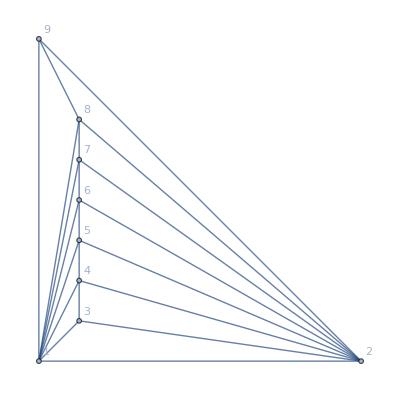

```mathematica
MinimalGraph[8]
```

```mathematica
IsomorphicGraphQ[MinimalGraph[8],ReadGrof[73]]
```

True

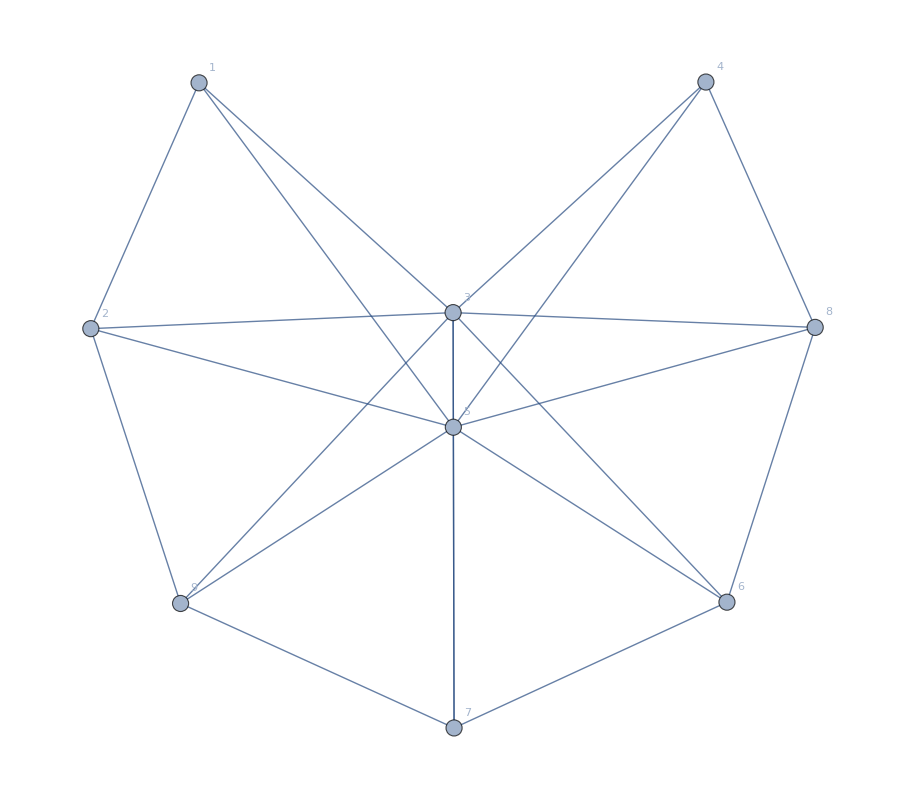

```mathematica
Graph[ReadGrof[73],VertexLabels->"Name"]
```

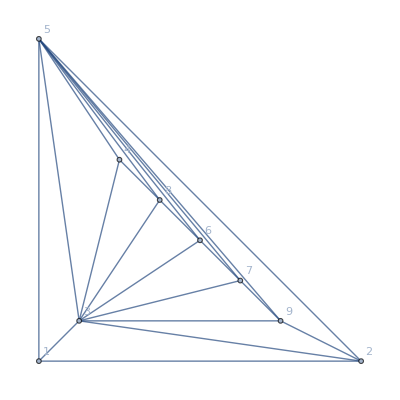

```mathematica
Graph[ReadGrof[73],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

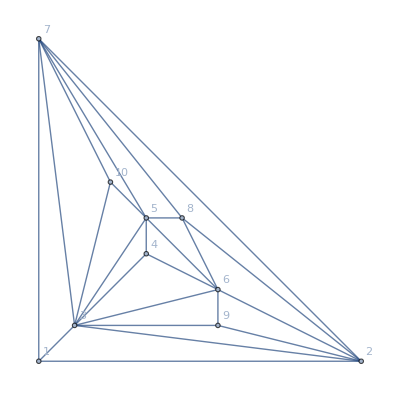

```mathematica
Graph[ReadGrof[297],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
Graph[ReadGrof[297],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]//FindFullFormula4
```

{v149ax25x38x67,v159x24ax38x67,v1489ax25x3x67,v16ax25x38x479}

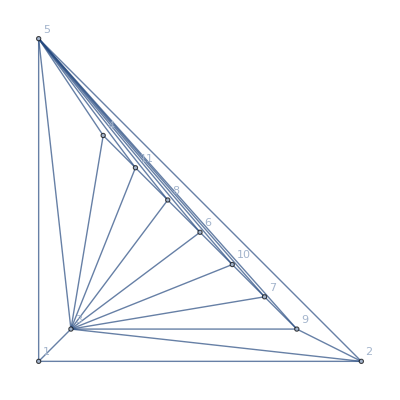

```mathematica
Graph[ReadGrof[1555],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
Graph[ReadGrof[1555],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]//FindFullFormula4
```

{v1489ax267bx3x5}